```mathematica
Nm=12;
μ0=-2.0;
ϵ=-1;
κ=0.1;
```

```mathematica
A[ϕ_]:= 2ϕ-1;
B[J_]:= Exp[-J];
```

```mathematica
μ[ϕ_,J_]:=2 Log[A[ϕ] √B[J]+√(1 + A[ϕ]^2(B[J]-1))]-Log[1-A[ϕ]^2]-J;
```

```mathematica
μr[ϕ_,nt_]:= μ0 + Log[nt - Nm ϕ + 1];
```

```mathematica
dμr[ϕ_,nt_]:= -Nm/(nt-Nm ϕ + 1);
dΩ[ϕ_,J_,nt_]:=μ[ϕ,J]+ϵ-(μr[ϕ,nt] +dμr[ϕ,nt]ϕ);
```

```mathematica
sRES=NDSolve[{ϕ'[t]==-κ dΩ[ϕ[t],-4,10],ϕ[0]==0.01},ϕ,{t,0,200}]
```

{{ϕ→InterpolatingFunction[…]}}

```mathematica
sSTALL = NDSolve[{ϕ'[t]==-κ dΩ[ϕ[t],-4,10],ϕ[0]==0.6},ϕ,{t,0,200}]
```

{{ϕ→InterpolatingFunction[…]}}

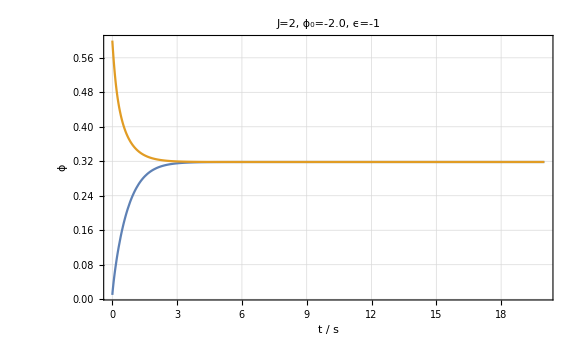

```mathematica
Plot[{Evaluate[ϕ[t]/.sRES],Evaluate[ϕ[t]/.sSTALL]},{t,0,20},PlotRange-> Full, ImageSize->Large,LabelStyle->{12,GrayLevel[0]}, Frame->True, GridLines->Automatic, FrameLabel->{"t / s","ϕ"}, PlotLabel->"J=2, ϕ_0=-2.0, ϵ=-1"]
```

```mathematica
.b4
```